## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
HBose[t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
HBose[t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]],{j,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j)]],{j,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

### Static density-density correlations

```mathematica
SiteNumberOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_density_static/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
```

```mathematica
Subscript[nn, corr]=Partition[Import[Subscript[fn, import]<>"_nn_corr.dat","Real64"],Subscript[L, val]]
Dimensions[%]
```

{{0.715028,0.399205,0.419169,0.419727,0.386325},{0.399205,0.807131,0.43508,0.455112,0.419727},{0.419169,0.43508,0.808332,0.435087,0.419176},{0.419727,0.455112,0.435087,0.807148,0.399229},{0.386325,0.419727,0.419176,0.399229,0.715041}}

{5,5}

```mathematica
(* check symmetry *)
Norm[Subscript[nn, corr]-Transpose[Subscript[nn, corr]]]
```

0.

```mathematica
Subscript[n, avr,A]=Import[Subscript[fn, import]<>"_n_avr_A.dat","Real64"]
Subscript[n, avr,B]=Import[Subscript[fn, import]<>"_n_avr_B.dat","Real64"]
```

{0.621547,0.675357,0.676026,0.675368,0.621558}

{0.621547,0.675357,0.676026,0.675368,0.621558}

```mathematica
(* should agree *)
Norm[Subscript[n, avr,A]-Subscript[n, avr,B]]
```

0.

```mathematica
(* cumulant *)
Subscript[nn, cum]=Subscript[nn, corr]-KroneckerProduct[Subscript[n, avr,A],Subscript[n, avr,B]];
```

```mathematica
(* reference calculation *)
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],H,expβH},H=N[HBose[tH,U,μ,M,L]];expβH=MatrixExp[-β H];Subscript[nn, corr,ref]=Table[Tr[expβH.SiteNumberOpFull[i-1,M,L].SiteNumberOpFull[j-1,M,L]]/Tr[expβH],{i,L},{j,L}];Subscript[n, avr,ref]=Table[Tr[expβH.SiteNumberOpFull[i-1,M,L]]/Tr[expβH],{i,L}]];
```

```mathematica
(* check symmetry *)
Norm[Subscript[nn, corr,ref]-Transpose[Subscript[nn, corr,ref]]]
```

0.

```mathematica
(* compare *)
Norm[Subscript[nn, corr]-Subscript[nn, corr,ref]]
Norm[Subscript[n, avr,A]-Subscript[n, avr,ref]]
Norm[Subscript[n, avr,B]-Subscript[n, avr,ref]]
```

0.0000241645

0.0000117817

0.0000117817

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

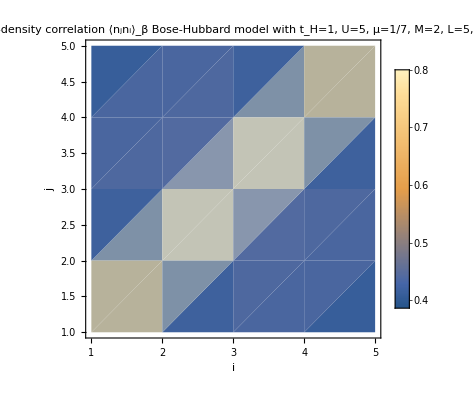

```mathematica
ListDensityPlot[Subscript[nn, corr],PlotLegends->Automatic,FrameLabel->{"i","j"},PlotLabel->"density-density correlation ⟨n_jn_i⟩_β\n"<>Subscript[plot, label]]
Export[Subscript[fn, export]<>"nn_corr_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

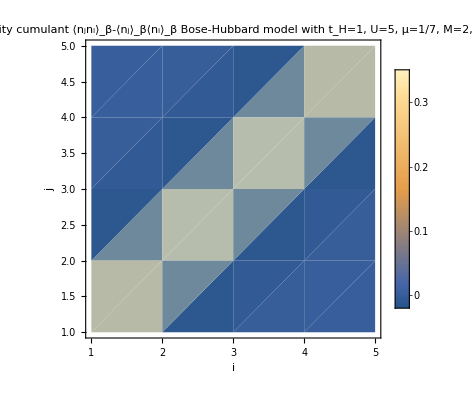

```mathematica
ListDensityPlot[Subscript[nn, cum],PlotLegends->Automatic,FrameLabel->{"i","j"},PlotLabel->"density-density cumulant ⟨n_jn_i⟩_β-⟨n_j⟩_β⟨n_i⟩_β\n"<>Subscript[plot, label]]
Export[Subscript[fn, export]<>"nn_cumulant_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

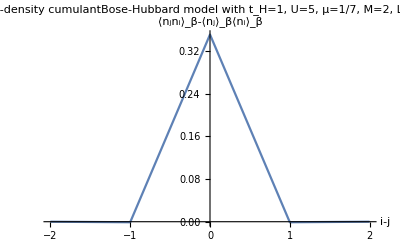

```mathematica
ListLinePlot[Transpose[{Range[-(Subscript[L, val]-1)/2,(Subscript[L, val]-1)/2],Diagonal[Reverse/@Subscript[nn, cum]]}],AxesLabel->{"i-j","⟨n_jn_i⟩_β-⟨n_j⟩_β⟨n_i⟩_β"},PlotLabel->"density-density cumulant"<>Subscript[plot, label]]
Export[Subscript[fn, export]<>"nn_cut_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.